```mathematica
β[ω,0.001,1,0]
```

{{(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0,0},{-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0,0},{0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0,0},{0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0,0},{0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0,0},{0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0},{0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0},{0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0},{0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0},{0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0},{0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1},{0,0,0,0,0,0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω}}

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[12]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[12]-A.T.J.T].A,13200];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-SL[ω,0.001,1,0].T[1].SR[ω,0.001,1,0].T[1]].SL[ω,0.001,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].SL[ω,0.001,1,0].T[1]].SR[ω,0.001,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,0.001,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

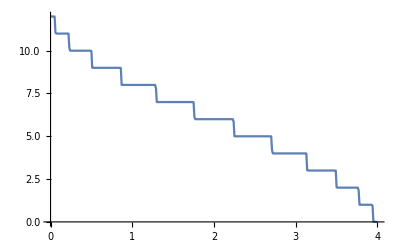
{1.12983,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
ξ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
ξ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
```

```mathematica
Clear[k614,k613,k612,k611,k610,k69,k68,k67,k66,k65,k64,k63,k62,k61]
```

```mathematica
k614[ω_,ϵ1_]:=k614[ω,ϵ1]=Append[{},Table[ξ14[ω,0.001,1,0,ϵ1],{100}]];
k613[ω_,ϵ1_]:=k613[ω,ϵ1]=Append[{},Table[ξ13[ω,0.001,1,0,ϵ1],{100}]];
k612[ω_,ϵ1_]:=k612[ω,ϵ1]=Append[{},Table[ξ12[ω,0.001,1,0,ϵ1],{100}]];
k611[ω_,ϵ1_]:=k611[ω,ϵ1]=Append[{},Table[ξ11[ω,0.001,1,0,ϵ1],{100}]];
k610[ω_,ϵ1_]:=k610[ω,ϵ1]=Append[{},Table[ξ10[ω,0.001,1,0,ϵ1],{100}]];
k69[ω_,ϵ1_]:=k69[ω,ϵ1]=Append[{},Table[ξ9[ω,0.001,1,0,ϵ1],{100}]];
k68[ω_,ϵ1_]:=k68[ω,ϵ1]=Append[{},Table[ξ8[ω,0.001,1,0,ϵ1],{100}]];
k67[ω_,ϵ1_]:=k67[ω,ϵ1]=Append[{},Table[ξ7[ω,0.001,1,0,ϵ1],{100}]];
k66[ω_,ϵ1_]:=k66[ω,ϵ1]=Append[{},Table[ξ6[ω,0.001,1,0,ϵ1],{100}]];
k65[ω_,ϵ1_]:=k65[ω,ϵ1]=Append[{},Table[ξ5[ω,0.001,1,0,ϵ1],{100}]];
k64[ω_,ϵ1_]:=k64[ω,ϵ1]=Append[{},Table[ξ4[ω,0.001,1,0,ϵ1],{100}]];
k63[ω_,ϵ1_]:=k63[ω,ϵ1]=Append[{},Table[ξ3[ω,0.001,1,0,ϵ1],{100}]];
k62[ω_,ϵ1_]:=k62[ω,ϵ1]=Append[{},Table[ξ2[ω,0.001,1,0,ϵ1],{100}]];
k61[ω_,ϵ1_]:=k61[ω,ϵ1]=Append[{},Table[ξ1[ω,0.001,1,0,ϵ1],{100}]]
```

```mathematica
ρ6[ω_,ϵ1_]:=Join[Mean[k61[ω,ϵ1]],Mean[k62[ω,ϵ1]],Mean[k63[ω,ϵ1]],Mean[k64[ω,ϵ1]],Mean[k65[ω,ϵ1]],Mean[k66[ω,ϵ1]],Mean[k67[ω,ϵ1]],Mean[k68[ω,ϵ1]],Mean[k69[ω,ϵ1]],Mean[k610[ω,ϵ1]],Mean[k611[ω,ϵ1]],Mean[k613[ω,ϵ1]],Mean[k614[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ6[.5,0.5]]]
```

{10.1381,7.04577}

```mathematica
Export["6imp3.csv",Table[{ω,Mean[ρ6[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

6imp3.csv

```mathematica
Export["6imp4.csv",Table[{ω,Mean[ρ6[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

6imp4.csv

```mathematica
Export["6imp5.csv",Table[{ω,Mean[ρ6[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

6imp5.csv

```mathematica
Export["6imp6.csv",Table[{ω,Mean[ρ6[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

6imp6.csv

```mathematica
Export["6imp7.csv",Table[{ω,Mean[ρ6[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

6imp7.csv

```mathematica
Export["6imp8.csv",Table[{ω,Mean[ρ6[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

6imp8.csv

```mathematica
Export["6imp9.csv",Table[{ω,Mean[ρ6[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

6imp9.csv

```mathematica
Export["6imp1.csv",Table[{ω,Mean[ρ6[ω,1]]},{ω,Range[0,4,0.01]}]]
```

6imp1.csv

```mathematica
λ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
λ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
λ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
λ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
λ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
λ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
λ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
```

```mathematica
Clear[k77,k76,k75,k74,k73,k72,k71]
```

```mathematica
k77[ω_,ϵ1_]:=k77[ω,ϵ1]=Append[{},Table[λ7[ω,0.001,1,0,ϵ1],{i,150}]];
k76[ω_,ϵ1_]:=k76[ω,ϵ1]=Append[{},Table[λ6[ω,0.001,1,0,ϵ1],{i,150}]];
k75[ω_,ϵ1_]:=k75[ω,ϵ1]=Append[{},Table[λ5[ω,0.001,1,0,ϵ1],{i,150}]];
k74[ω_,ϵ1_]:=k74[ω,ϵ1]=Append[{},Table[λ4[ω,0.001,1,0,ϵ1],{i,150}]];
k73[ω_,ϵ1_]:=k73[ω,ϵ1]=Append[{},Table[λ3[ω,0.001,1,0,ϵ1],{i,150}]];
k72[ω_,ϵ1_]:=k72[ω,ϵ1]=Append[{},Table[λ2[ω,0.001,1,0,ϵ1],{i,150}]];
k71[ω_,ϵ1_]:=k71[ω,ϵ1]=Append[{},Table[λ1[ω,0.001,1,0,ϵ1],{i,150}]]
```

```mathematica
ρ7[ω_,ϵ1_]:=Join[Mean[k71[ω,ϵ1]],Mean[k72[ω,ϵ1]],Mean[k73[ω,ϵ1]],Mean[k74[ω,ϵ1]],Mean[k75[ω,ϵ1]],Mean[k76[ω,ϵ1]],Mean[k77[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ7[1.5,0.5]]]
```

{7.36751,6.69469}

```mathematica
Export["7imp3.csv",Table[{ω,Mean[ρ7[ω,0.3]]},{ω,Range[0,4,0.01]}]]
Export["7imp4.csv",Table[{ω,Mean[ρ7[ω,0.4]]},{ω,Range[0,4,0.01]}]]
Export["7imp5.csv",Table[{ω,Mean[ρ7[ω,0.5]]},{ω,Range[0,4,0.01]}]]
Export["7imp6.csv",Table[{ω,Mean[ρ7[ω,0.6]]},{ω,Range[0,4,0.01]}]]
Export["7imp7.csv",Table[{ω,Mean[ρ7[ω,0.7]]},{ω,Range[0,4,0.01]}]]
Export["7imp8.csv",Table[{ω,Mean[ρ7[ω,0.8]]},{ω,Range[0,4,0.01]}]]
Export["7imp9.csv",Table[{ω,Mean[ρ7[ω,0.9]]},{ω,Range[0,4,0.01]}]]
Export["7imp1.csv",Table[{ω,Mean[ρ7[ω,1]]},{ω,Range[0,4,0.01]}]]
```

7imp3.csv

7imp4.csv

7imp5.csv

7imp6.csv

7imp7.csv

7imp8.csv

7imp9.csv

7imp1.csv

```mathematica
ϕϕ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,0.001,1,0]],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}], μ8=RandomInteger[{1,12}]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[12]-imp1.T[1].SL[ω,0.001,1,0].T[1]].imp1;
Sl12:=Inverse[IdentityMatrix[12]-imp2.T[1].Sl11.T[1]].imp2;
Sl13:=Inverse[IdentityMatrix[12]-imp3.T[1].Sl12.T[1]].imp3;
Sl14:=Inverse[IdentityMatrix[12]-imp4.T[1].Sl13.T[1]].imp4;
Sl15:=Inverse[IdentityMatrix[12]-imp5.T[1].Sl14.T[1]].imp5;
Sl16:=Inverse[IdentityMatrix[12]-imp6.T[1].Sl15.T[1]].imp6;
Sl17:=Inverse[IdentityMatrix[12]-imp7.T[1].Sl16.T[1]].imp7;
Sl18:=Inverse[IdentityMatrix[12]-imp8.T[1].Sl17.T[1]].imp8;
Il1:=Inverse[IdentityMatrix[12]-Sl18.T[1].SR[ω,0.001,1,0].T[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.001,1,0].T[1].Sl18.T[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T[1].grr1.T[1]-T[1].GNON1.T[1].GNON1]]]
```

```mathematica
k8[ω_,ϵ1_]:=k8[ω,ϵ1]=Mean[Append[{},Table[ϕϕ[ω,0.001,1,0,ϵ1],{i,1500}]]]
```

```mathematica
ρ8[ω_,ϵ1_]:=k8[ω,ϵ1]
```

```mathematica
Timing[Mean[k8[0,0.7]]]
```

{11.6167,6.07038}

```mathematica
Export["8imp3.csv",Table[{ω,Mean[ρ8[ω,0.3]]},{ω,Range[0,4,0.01]}]]
Export["8imp4.csv",Table[{ω,Mean[ρ8[ω,0.4]]},{ω,Range[0,4,0.01]}]]
Export["8imp5.csv",Table[{ω,Mean[ρ8[ω,0.5]]},{ω,Range[0,4,0.01]}]]
Export["8imp6.csv",Table[{ω,Mean[ρ8[ω,0.6]]},{ω,Range[0,4,0.01]}]]
Export["8imp7.csv",Table[{ω,Mean[ρ8[ω,0.7]]},{ω,Range[0,4,0.01]}]]
Export["8imp8.csv",Table[{ω,Mean[ρ8[ω,0.8]]},{ω,Range[0,4,0.01]}]]
Export["8imp9.csv",Table[{ω,Mean[ρ8[ω,0.9]]},{ω,Range[0,4,0.01]}]]
Export["8imp1.csv",Table[{ω,Mean[ρ8[ω,1]]},{ω,Range[0,4,0.01]}]]
```

8imp3.csv

8imp4.csv

8imp5.csv

8imp6.csv

8imp7.csv

8imp8.csv

8imp9.csv

8imp1.csv

```mathematica
SystemOpen["8imp1.csv"]
```

$Failed